## Visualización de listas

ListPlot es una manera de mostrar, o visualizar, una lista de números. Hay muchas otras maneras, según las características que se quieran destacar en dicha lista.

ListLinePlot presenta el gráfico de una lista, uniendo los valores:

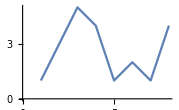

```mathematica
ListLinePlot[{1,3,5,4,1,2,1,4}]
```

Cuando los valores saltan de un lado a otro, puede ser difícil ver lo que sucede si no se unen con segmentos:

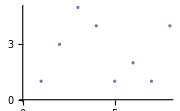

```mathematica
ListPlot[{1,3,5,4,1,2,1,4}]
```

También puede ser útil mostrar un diagrama de barras:

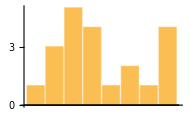

```mathematica
BarChart[{1,3,5,4,1,2,1,4}]
```

Si la lista no es demasiado grande, puede usarse un diagrama circular:

```mathematica
PieChart[{1,3,5,4}]
```

-Graphics-

Si solo interesa saber qué números aparecen, pueden presentarse gráficamente sobre una recta numérica:

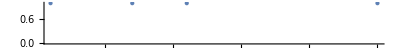

```mathematica
NumberLinePlot[{1,7,11,25}]
```

En ocasiones no se requiere un diagrama, sino solo presentar los elementos de una lista en forma de columna:

```mathematica
Column[{100,350,502,400}]
```

100
350
502
400

Las listas pueden contener cosas cualesquiera, incluyendo diagramas. Así, se pueden combinar varios diagramas poniéndolos en una lista.

Hacer una lista de dos diagramas circulares:

```mathematica
{PieChart[Range[3]],PieChart[Range[5]]}
```

{-Graphics-,-Graphics-}

Muestre juntos tres diagramas de barras:

```mathematica
{BarChart[{1,1,4,2}],BarChart[{5,1,1,0}],BarChart[{1,3,2,4}]}
```

{-Graphics-,-Graphics-,-Graphics-}

Vocabulario

ListLinePlot[{1,2,5}] |   | valores unidos por segmentos de recta
BarChart[{1,2,5}] |   | diagrama de barras (los valores dan la altura de las barras) 
PieChart[{1,2,5}] |   | diagrama circular (los valores dan el tamaño de los sectores) 
NumberLinePlot[{1,2,5}] |   | números colocados sobre una recta 
Column[{1,2,5}] |   | elementos exhibidos en una columna

"7 Exercises Available"
"with 6 extras" | "Get Started »"

Construya un diagrama de barras con {1,1,2,3,5}. »

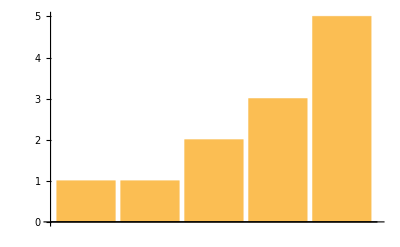
| Expected output: |  
  | -Graphics- |

Produzca un diagrama circular con los números del 1 al 10. »

| Expected output: |  
  | -Graphics- |

Forme un diagrama de barras de los números consecutivos del 20 al 1. »

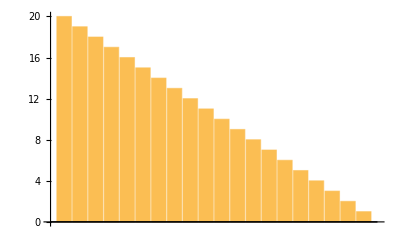
| Expected output: |  
  | -Graphics- |

Muestre en una columna los números del 1 al 5. »

| Expected output: |  
  | 1
2
3
4
5 |

Presente los cuadrados {1,4,9,16,25} sobre una recta numérica. »

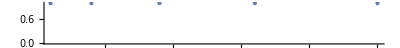
| Expected output: |  
  | -Graphics- |

Forme un gráfico circular con 10 sectores idénticos, cada uno de tamaño 1. »

| Expected output: |  
  | -Graphics- |

Presente una columna de los gráficos circulares con 1, 2 y 3 sectores idénticos. »

| Expected output: |  
  | -Graphics- |

Forme una lista de gráficos circulares con 1, 2 y 3 sectores idénticos. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Presente un diagrama de barras con la secuencia 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1. »

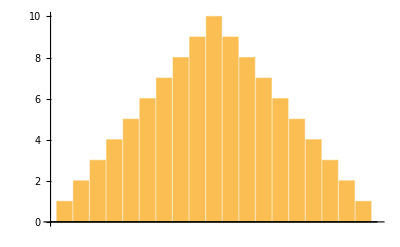
| Expected output: |  
  | -Graphics- |

Muestre una lista con un diagrama circular, un diagrama de barras y un gráfico con los valores unidos, de los números del 1 al 10. »

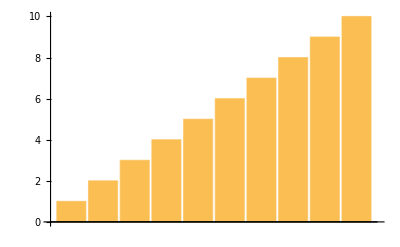
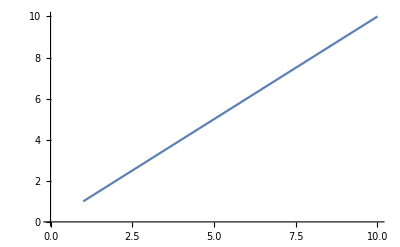
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Muestre una lista con un diagrama circular y un diagrama de barras de {1,1,2,3,5,8,13,21,34,55}. »

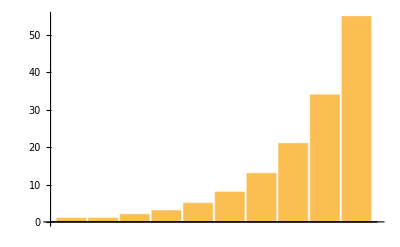
| Expected output: |  
  | {-Graphics-,-Graphics-} |

Forme una columna de 2 diagramas con dos presentaciones de números sobre la recta numérica de {1,2,3,4,5}. »

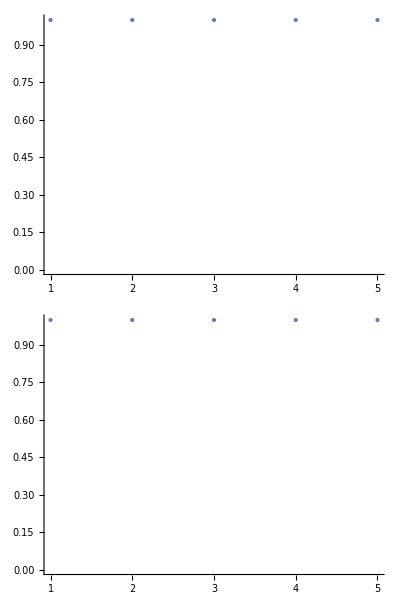
| Expected output: |  
  | -Graphics- |

Presente una recta numérica con las fracciones 1/2, 1/3, ... hasta 1/9. »

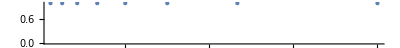
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Cómo funcionan los diagramas circulares en Wolfram Language?

Como en cualquier diagrama circular, los tamaños relativos de los sectores están determinados por los tamaños relativos de los números en la lista. En Wolfram Language, el sector correspondiente al primer número comienza en la posición de las 9:00 en un reloj y los sectores subsecuentes se acomodan en el sentido de las manecillas. Los colores de los sectores se eligen en una secuencia definida.

¿Cómo se determina la escala vertical en las representaciones gráficas?

Esto se hace de manera que se incluyan automáticamente todos los puntos, excepto valores atípicos distantes. Más adelante (Sección 20), se hablará de la opción PlotRange, que permite especificar exactamente de dónde a dónde se presentará el gráfico.

Nota técnica

Especialmente a quienes estén familiarizados con otros lenguajes de computación, les podrá sonar extraño, por ejemplo, que aparezca una lista de gráficos como resultado de un proceso de cómputo. Esto es posible debido al hecho crucial de que Wolfram Language es simbólico. Y, por cierto, también podrán aparecer gráficos como parte de alguna entrada.

Para explorar más

Visualización de datos en Wolfram Language »

Producción de gráficos y visualización de información en Wolfram Language »